```mathematica
(* this is used to get an analytic approximation for the GT charge of Na, Ca and Cl *)
```

```mathematica
Quit[]
```

```mathematica
rintqCafull=Import["/Users/anggao/Desktop/Na_Ca_Cl_potentials/intq_Ca_full.txt","Table"];
```

```mathematica
fintqCafull=Interpolation[rintqCafull]
```

InterpolatingFunction[{{0.002,2.}},<>]

```mathematica
ϵ=71
```

71

```mathematica
Qca=2
```

2

```mathematica
Qcashield=-Qca(1-1/ϵ)
```

-140/71

```mathematica
fintqCafullextended[r_]:=Piecewise[{{fintqCafull[r], r<1.99}, {Qcashield, r≥1.99}}]
```

InterpolatingFunction::dmval: Input value {0.000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

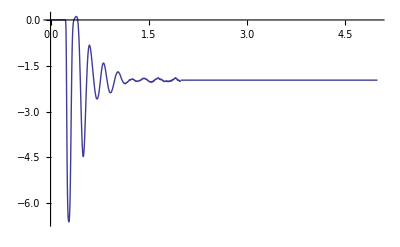

```mathematica
Plot[fintqCafullextended[r],{r,0,5},PlotRange->Full]
```

```mathematica
rintqCasc=Import["/Users/anggao/Desktop/Na_Ca_Cl_potentials/intq_Ca_0.txt","Table"];
```

```mathematica
fintqCasc=Interpolation[rintqCasc]
```

InterpolatingFunction[{{0.002,4.9}},<>]

InterpolatingFunction::dmval: Input value {0.0000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

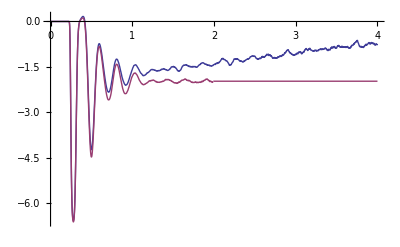

```mathematica
Plot[{fintqCasc[r],fintqCafullextended[r]},{r,0,4},PlotRange->Full]
```

```mathematica
dCa=0.2
```

0.2

```mathematica
sCa=6
```

6

```mathematica
fCacorrect[r_]:=Piecewise[{{0, r<dCa}, {Qcashield Erf[(r-dCa)/sCa], r≥dCa}}]
```

InterpolatingFunction::dmval: Input value {0.0000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

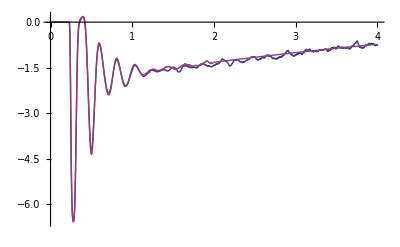

```mathematica
Plot[{fintqCasc[r],fintqCafullextended[r]-fCacorrect[r]},{r,0,4},PlotRange->Full]
```

```mathematica
(* Now let us start Na *)
```

```mathematica
rintqNafull=Import["/Users/anggao/Desktop/Na_Ca_Cl_potentials/intq_Na_full.txt","Table"];
```

```mathematica
fintqNafull=Interpolation[rintqNafull]
```

InterpolatingFunction[{{0.002,2.}},<>]

```mathematica
Qna=1
```

1

```mathematica
Qnashield=-Qna(1-1/ϵ)
```

-70/71

```mathematica
fintqNafullextended[r_]:=Piecewise[{{fintqNafull[r], r<1.99}, {Qnashield, r≥1.99}}]
```

InterpolatingFunction::dmval: Input value {0.000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

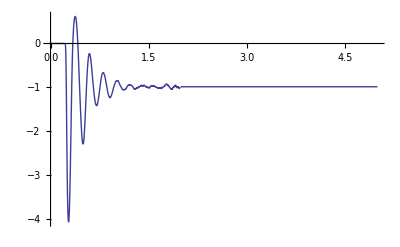

```mathematica
Plot[fintqNafullextended[r],{r,0,5},PlotRange->Full]
```

```mathematica
rintqNasc=Import["/Users/anggao/Desktop/Na_Ca_Cl_potentials/intq_Na_0.txt","Table"];
```

```mathematica
fintqNasc=Interpolation[rintqNasc]
```

InterpolatingFunction[{{0.002,4.9}},<>]

InterpolatingFunction::dmval: Input value {0.0000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

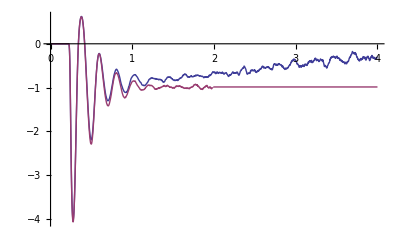

```mathematica
Plot[{fintqNasc[r],fintqNafullextended[r]},{r,0,4},PlotRange->Full]
```

```mathematica
dNa=0.2
```

0.2

```mathematica
sNa=6
```

6

```mathematica
fNacorrect[r_]:=Piecewise[{{0, r<dNa}, {Qnashield Erf[(r-dNa)/sNa], r≥dNa}}]
```

InterpolatingFunction::dmval: Input value {0.0000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

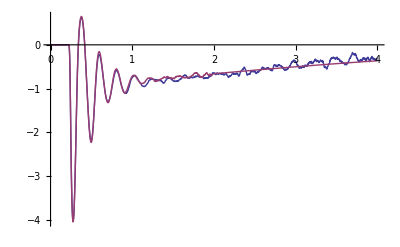

```mathematica
Plot[{fintqNasc[r],fintqNafullextended[r]-fNacorrect[r]},{r,0,4},PlotRange->Full]
```

```mathematica
(* the result for Na is doubtful, the GT charge density has too many fluctuations *)
```

```mathematica
(* Now let us start Cl *)
```

```mathematica
rintqClfull=Import["/Users/anggao/Desktop/Na_Ca_Cl_potentials/intq_Cl_full.txt","Table"];
```

```mathematica
fintqClfull=Interpolation[rintqClfull]
```

InterpolatingFunction[{{0.002,2.}},<>]

```mathematica
Qcl=-1
```

-1

```mathematica
Qclshield=-Qcl(1-1/ϵ)
```

70/71

```mathematica
fintqClfullextended[r_]:=Piecewise[{{fintqClfull[r], r<1.99}, {Qclshield, r≥1.99}}]
```

InterpolatingFunction::dmval: Input value {0.000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

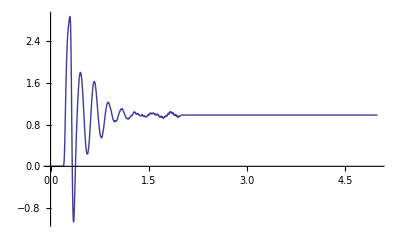

```mathematica
Plot[fintqClfullextended[r],{r,0,5},PlotRange->Full]
```

```mathematica
rintqClsc=Import["/Users/anggao/Desktop/Na_Ca_Cl_potentials/intq_Cl_0.txt","Table"];
```

```mathematica
fintqClsc=Interpolation[rintqClsc]
```

InterpolatingFunction[{{0.002,4.9}},<>]

InterpolatingFunction::dmval: Input value {0.0000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

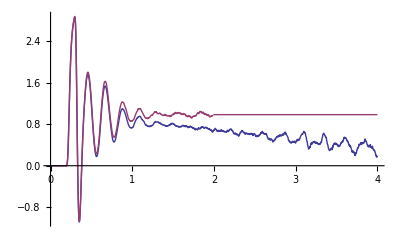

```mathematica
Plot[{fintqClsc[r],fintqClfullextended[r]},{r,0,4},PlotRange->Full]
```

```mathematica
dCl=0.2
```

0.2

```mathematica
sCl=6
```

6

```mathematica
fClcorrect[r_]:=Piecewise[{{0, r<dCl}, {Qclshield Erf[(r-dCl)/sCl], r≥dCl}}]
```

InterpolatingFunction::dmval: Input value {0.0000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

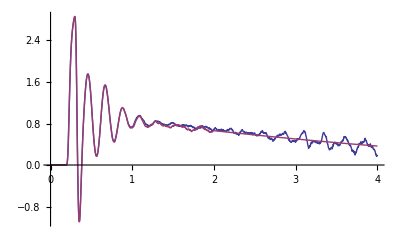

```mathematica
Plot[{fintqClsc[r],fintqClfullextended[r]-fClcorrect[r]},{r,0,4},PlotRange->Full]
```